# IC ALL TAXA

## INTRO CODE

```mathematica
(*ClearAll["Global`*"];*)
```

```mathematica
<<PollyMorphometrics`
<<PollyPhylogenetics`
<<PollyModularity`
```

PollyMorphometrics 12.2
(c) P. David Polly, 5 March 2017

Phylogenetics for Mathematica 5.0
(c) P. David Polly, 21 January 2018

Modularity for Mathematica 2.0
(c) P. David Polly and A. Goswami, 20 Dec 2010
Updated 7 April 2018.

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
AllTaxa={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
```

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
UlnaLabels=UlnaData[[1,1;;,1]];
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
ManusLabels=ManusData[[1;;,1]];
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
HumerusLabels=HumerusData[[1,1;;,1]];
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
TarsoLabels=TarsoData[[1,1;;,1]];
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
TibioLabels=TibioData[[1,1;;,1]];
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
FemurLabels=FemurData[[1,1;;,1]];
x=1;
UlnaLabelsList=Table[StringSplit[UlnaLabels[[x]],"_"][[1;;2]], {x,Length[UlnaLabels]}];
ManusLabelsList=Table[StringSplit[ManusLabels[[x]],"_"][[1;;2]], {x,Length[ManusLabels]}];
HumerusLabelsList=Table[StringSplit[HumerusLabels[[x]],"_"][[1;;2]], {x,Length[HumerusLabels]}];
FemurLabelsList=Table[StringSplit[FemurLabels[[x]],"_"][[1;;2]], {x,Length[FemurLabels]}];
TibioLabelsList=Table[StringSplit[TibioLabels[[x]],"_"][[1;;2]], {x,Length[TibioLabels]}];
TarsoLabelsList=Table[StringSplit[TarsoLabels[[x]],"_"][[1;;2]], {x,Length[TarsoLabels]}];
ForeLimb=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,2]]];
HindLimb=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,2]]];
```

```mathematica
Complement[Union[HumerusLabelsList[[1;;,1]]],Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]]]
```

{BermudaFLDuck,DarwinsRhea,InaccessibleIsRail,LittleTin,RdrgsSolitaire,UndulatedTin,YllwLggdTin}

```mathematica
Union[HumerusLabelsList[[1;;,1]]]
```

{AmericanCoot,AmericanKestrel,AndeanTin,BaldEagle,BermudaFLDuck,Budgie,BuffBanRail,ChileanTin,ChubutSD,Cockatiel,CommonGoldeneye,DarwinsNothura,DarwinsRhea,DblCrstdCormorant,ElegCrstdTin,Emu,FalklandSD,FlgtlessCormorant,FlyingSD,FuegianSD,GiantCoot,GreaterRhea,GreatTin,GuamRail,Gull,Hoatzin,HornedGrebe,Ibis,InaccessibleIsRail,IndianPeafowl,JuninGrebe,Kakapo,Kea,KingBoP,LaysanRail,LittleTin,LordHoweRail,MagnificentBoP,Nene,NIsTakahe,NZMerganser,Ostrich,P.lemoinei,RdrgsSolitaire,RedLggdSeriema,RockPigeon,RuffedGrouse,SBKiwi,SCassowary,ShrtTldShearwater,Sora,SpottedNothura,StripedManakin,TasNativehen,TiticacaGrebe,TristanMoorhen,UndulatedTin,Weka,YllwCrwndAmazon,YllwLggdTin}

## TARSOMETATARSUS

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Tarso/FL only/Tarso FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Tarso/F only/Tarso F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TarsoProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[TarsoLabelsList,#]]&/@HindLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=TarsoLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
TarsoProc1=Procrustes[means3, 200, 2];
```

### Scores of TarsoProc:

```mathematica
Consensus=Mean[TarsoProc];
resids=#-Consensus&/@TarsoProc;
P=Covariance[TarsoProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TarsoProc (& also "scores"):

```mathematica
Fpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@F]];
FLpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@FL]];
```

### Dividing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlyingTree,Transpose[{Union[shortlabels][[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingTarsoProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlightlessTree,Transpose[{Union[shortlabels][[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessTarsoProc=FlightlessICproc;
```

### Making covariance matrices:

```mathematica
FLCovIC=Covariance[FlightlessICproc];
FCovIC=Covariance[FlyingICproc];
```

```mathematica
TarsoTaxaF=Union[shortlabels][[Fpos]];
TarsoTaxaFL=Union[shortlabels][[FLpos]];
```

## Mantel Test

```mathematica
(*Timing[MantelForMorphometrics[FLCovIC,FCovIC,10000]]
Speak["Mantel for tarso is finished"]*)
```

{327.741,{0.318437,0.}}

{327.741,{0.318437,0.}}

## CPCA

```mathematica
Labels=Join[ConstantArray["flying",Length[FlyingICproc]],ConstantArray["flightless",Length[FlightlessICproc]]];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICTarsoAllTaxa_NoGeneric_Scores.csv",Join[FlyingICscores,FlightlessICscores]*1000,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICTarsoAllTaxa_NoGeneric_labels.csv",Labels,"CSV"];
```

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaTarso_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaTarso_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaTarso_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Tarsoexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flightless | 20.1195 | 67.2179 | 4.01248 | 1.46919 | 0.929652 | 0.539624 | 2.44439 | 0.179727 | 0.0820646 | 0.0581365
flying | 69.335 | 2.10313 | 8.44784 | 3.35919 | 2.93081 | 4.75412 | 1.09226 | 0.775384 | 2.35559 | 1.54419)

```mathematica
Tarsolambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Tarsoloadings=ICTarsoCPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

### Images

```mathematica
(*Tarsocpc1=Table[
Test=(vectors[[1;;,1;;Length[ICTarsoCPCAloadings]-1]].ICTarsoCPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

```mathematica
(*Tarsocpc2=Table[
Test=(vectors[[1;;,1;;Length[ICTarsoCPCAloadings]-1]].ICTarsoCPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

### CPCA EV Comparison

```mathematica
X=1;
fEV=Table[Variance[Transpose[FlyingICscores][[X]]],{X,Length[Transpose[FlyingICscores]]}];
```

```mathematica
X=1;
flEV=Table[Variance[Transpose[FlightlessICscores][[X]]],{X,Length[Transpose[FlightlessICscores]]}];
```

```mathematica
TarsoICcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],AccountingForm[fEV[[1;;10]]],AccountingForm[CPCAlambda[[3,2;;11]],11],AccountingForm[flEV[[1;;10]]]};
TarsoICcpcaEV
```

{{0.000227024,0.000758473,0.000045276,0.000016578,0.00001049,0.000006089,0.000027582,0.000002028,0.000000926,0.000000656},{0.000193148,0.0000307253,0.0000105285,0.0000121024,0.00000869141,0.00000688328,0.00000798334,0.00000483829,0.00000269958,0.00000263424},{0.000200212,0.000006073,0.000024394,0.0000097,0.000008463,0.000013728,0.000003154,0.000002239,0.000006802,0.000004459},{0.000242398,0.000234942,0.000161263,0.0000177706,0.0000151197,0.0000910441,0.00016075,0.0000150942,0.0000506829,0.00000835872}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

1.11974

```mathematica
VectorAngle[CPCAlambda[[3,2;;6]],flEV[[1;;5]]]
```

0.774138

## Eigenvalue Dispersion

### Intro

```mathematica
<<HierarchicalClustering`
Modularity[Landmarks_,NLands_,NDims_,Labels_,Randomization_:"False"]:=Module[{superimposed,residuals,P2,EVStdev2,Plot2,NinetyFivePercentCutoff2,Tree2,EV2,BootEV2,MaxMinBootEV2,MeanBootEV1,MeanBootEV2,
Rows,Columns,dims,NumMods2,RelEVStdev2,ModulePicture},
superimposed=Procrustes[Landmarks,NLands,NDims];
superimposed=Partition[Partition[Flatten[superimposed],NDims],NLands];
{Rows,Columns,dims}=Dimensions[superimposed];
P2=CanonicalCorrelation[superimposed];
EV2=Chop[Eigenvalues[P2]];
EVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]];
RelEVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]]/Sqrt[MatrixRank[P2]];


If[Randomization=="RandomizationTest",
BootEV2=Table[Eigenvalues[CanonicalCorrelation[Partition[superimposed[[#[[1]],#[[2]]]]&/@Flatten[ Table[Table[{RandomInteger[{1,Rows}],RandomInteger[{1,Columns}]},{Columns}],{Rows}],1],NLands]]],{100}];
MaxMinBootEV2=Chop[Transpose[{Max[#]&/@Transpose[BootEV2],Min[#]&/@Transpose[BootEV2]}]];
MeanBootEV2=Chop[Mean[#]&/@Transpose[BootEV2]];
NumMods2=Length[Select[EV2-(#[[1]]&/@MaxMinBootEV2),Positive]];
If[NumMods2==0,NumMods2=1];
Plot2=Graphics[{
{Gray,Table[Rectangle[{x-.45,0},{x+.45,EV2[[x]]}],{x,Length[EV2]}]},
{Black,AbsoluteThickness[2],Dashed,Table[Line[{{x,MaxMinBootEV2[[x,2]]},{x,MaxMinBootEV2[[x,1]]}}],{x,Length[MaxMinBootEV2]}]},
{Black,AbsolutePointSize[5],Table[Point[{x,MeanBootEV2[[x]]}],{x,Length[MeanBootEV2]}]}
},PlotLabel->"Eigenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&),HighlightLevel->NumMods2];

clust=Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"];
If[NumMods2>1,splitClusts=ClusterSplit[clust,NumMods2]];

If[NumMods2<2,
AllComas=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[clust],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[1<NumMods2<3,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[2<NumMods2<4,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[3<NumMods2<5,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[NumMods2<2,TipPos=Flatten[Position[AllComas,#]&/@Labels];
Tips=FromRomanNumeral[AllComas[[Sort[TipPos]]]];];

If[1<NumMods2<3,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
AllTips={Tips1,Tips2};
CorrectTips=AllTips;];

If[2<NumMods2<4,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
AllTips={Tips1,Tips2,Tips3};
CorrectTips=AllTips;];

If[3<NumMods2<5,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
AllTips={Tips1,Tips2,Tips3,Tips4};
CorrectTips=AllTips;];

If[NumMods2<2,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[Tips]]]}
}
]];
If[1<NumMods2<3,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]}
}
];];
If[2<NumMods2<4,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]}
}
];];
If[3<NumMods2<5,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]}
}
];];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eignvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{"Estimated Number of Modules: "<>ToString[NumMods2]},
(*{Plot2,Tree2,ModulePicture},*)
{Plot2,Tree2,ModulePicture}
},Alignment->Left],FontFamily->"Helvetica"]
]
,

Plot2=BarChart[EV2,PlotLabel->"Eigvenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&)];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eigenvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{Plot2,Tree2}
},Alignment->Left],FontFamily->"Helvetica"]
]

];



]
```

### Rest of Code

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingICproc,200,2,Labels,"RandomizationTest"];
TaFMod=FMod;
mod=FMod[[1,1,3;;6]];
TarsoFed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessICproc,200,2,Labels,"RandomizationTest"];
TaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
TarsoFLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
(*brokeoutlines[[15]]*)
```

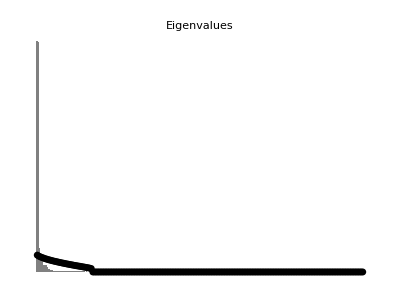
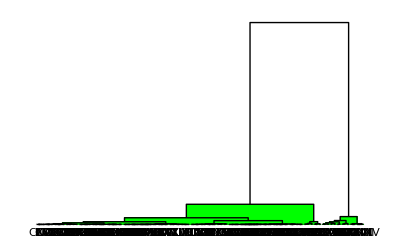
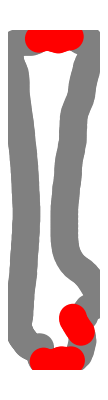
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 25.7902 |  | 
Relative Eigenvalue SD: 4.42298 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
(*brokeoutlines[[7]]*)
```

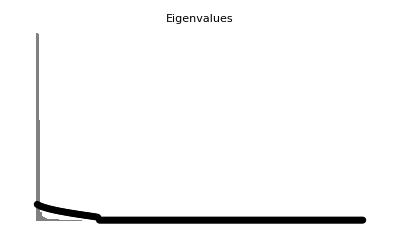
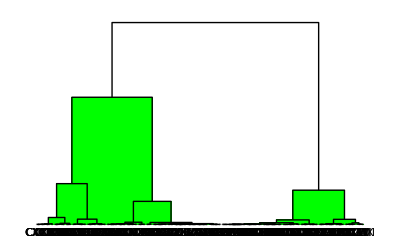
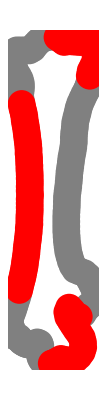
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 22.228 |  | 
Relative Eigenvalue SD: 3.60586 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.160128 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

```mathematica
TarsoED=Partition[Join[getcolumnbTitles,TarsoFed,TarsoFLed],5];
(*TarsoED//MatrixForm*)
```

## TIBIOTARSUS

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Tibia/FL only/Tibia FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Tibia/F only/Tibia F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TibioProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[TibioLabelsList,#]]&/@HindLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=TibioLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
TibioProc1=Procrustes[means3, 200, 2];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[TibioProc];
resids=#-Consensus&/@TibioProc;
P=Covariance[TibioProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
Fpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@F]];
FLpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@FL]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlyingTree,Transpose[{Union[shortlabels][[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingTibioProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlightlessTree,Transpose[{Union[shortlabels][[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessTibioProc=FlightlessICproc;
```

### Making covariance matrices:

```mathematica
FLCovIC=Covariance[FlightlessICproc];
FCovIC=Covariance[FlyingICproc];
```

```mathematica
TibiaTaxaF=Union[shortlabels][[Fpos]];
TibiaTaxaFL=Union[shortlabels][[FLpos]];
```

## Mantel Test

```mathematica
(*Timing[MantelForMorphometrics[FLCovIC,FCovIC,10000]]
Speak["Mantel for tibia is finished"]*)
```

{331.848,{0.463483,0.}}

{331.848,{0.463483,0.}}

## CPCA

```mathematica
Labels=Join[ConstantArray["flying",Length[FlyingICproc]],ConstantArray["flightless",Length[FlightlessICproc]]];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICTibiaAllTaxa_NoGeneric_Scores.csv",Join[FlyingICscores,FlightlessICscores]*1000,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICTibiaAllTaxa_NoGeneric_labels.csv",Labels,"CSV"];
```

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaTibia_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaTibia_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaTibia_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Tibiaexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flightless | 32.2249 | 6.63749 | 49.7845 | 3.79495 | 1.58937 | 0.27389 | 1.05921 | 1.29584 | 0.202539 | 0.578488
flying | 48.4329 | 27.5475 | 1.7291 | 5.45831 | 4.39845 | 4.3182 | 1.4823 | 0.393665 | 1.34149 | 0.423947)

```mathematica
Tibialambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Tibialoadings=icCPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*x=1;
Table[
Test=(vectors[[1;;,1;;Length[icCPCAloadings]-1]].icCPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

### CPCA EV Comparison

```mathematica
X=1;
fEV=Table[Variance[Transpose[FlyingICscores][[X]]],{X,Length[Transpose[FlyingICscores]]}];
```

```mathematica
X=1;
flEV=Table[Variance[Transpose[FlightlessICscores][[X]]],{X,Length[Transpose[FlightlessICscores]]}];
```

```mathematica
TibiaICcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],AccountingForm[fEV[[1;;10]]],AccountingForm[CPCAlambda[[3,2;;11]],11],AccountingForm[flEV[[1;;10]]]};
TibiaICcpcaEV
```

{{0.000142717,0.000029396,0.000220485,0.000016807,0.000007039,0.000001213,0.000004691,0.000005739,0.000000897,0.000002562},{0.0000322188,0.000015977,0.00000516339,0.00000292702,0.00000183651,0.00000310961,0.000000888691,0.00000137657,0.000000880662,0.000000449155},{0.000031988,0.000018194,0.000001142,0.000003605,0.000002905,0.000002852,0.000000979,0.00000026,0.000000886,0.00000028},{0.000112008,0.0000261366,0.000165708,0.0000443966,0.00000851462,0.0000153313,0.0000219346,0.00000200017,0.0000108638,0.00000826725}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.865364

```mathematica
VectorAngle[CPCAlambda[[3,2;;6]],flEV[[1;;5]]]
```

0.954721

```mathematica
VectorAngle[CPCAlambda[[2,2;;3]],fEV[[1;;2]]]
```

0.257223

```mathematica
VectorAngle[CPCAlambda[[3,2;;3]],flEV[[1;;2]]]
```

0.2879

## Eigenvalue Dispersion

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingICproc,200,2,Labels,"RandomizationTest"];
TiFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessICproc,200,2,Labels,"RandomizationTest"];
TiFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
TibiaED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*TibiaED//MatrixForm*)
```

```mathematica
(*brokeoutlines[[18]]*)
```

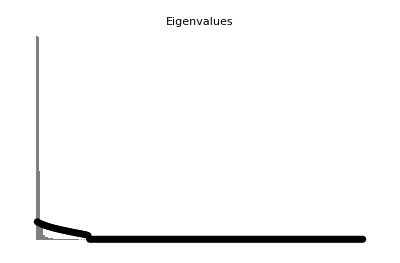
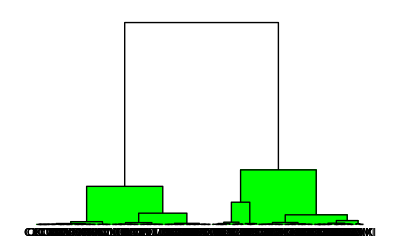
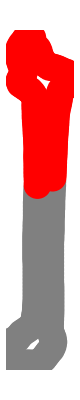
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 24.5723 |  | 
Relative Eigenvalue SD: 4.34382 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
(*brokeoutlines[[8]]*)
```

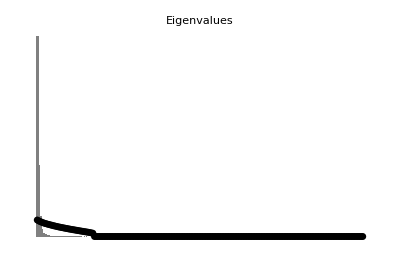
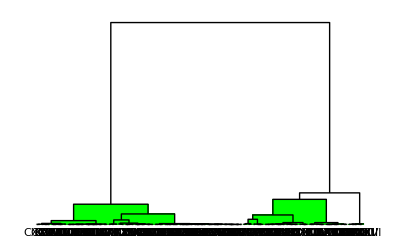
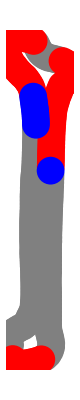
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 23.3586 |  | 
Relative Eigenvalue SD: 3.94832 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.166667 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

## FEMUR

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Femur/FL only/Femur FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Femur/F only/Femur F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[FemurLabelsList,#]]&/@HindLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=FemurLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
FemurProc1=Procrustes[means3, 200, 2];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[FemurProc];
resids=#-Consensus&/@FemurProc;
P=Covariance[FemurProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
Fpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@F]];
FLpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@FL]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlyingTree,Transpose[{Union[shortlabels][[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingFemurProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlightlessTree,Transpose[{Union[shortlabels][[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessFemurProc=FlightlessICproc;
```

### Making covariance matrices:

```mathematica
FLCovIC=Covariance[FlightlessICproc];
FCovIC=Covariance[FlyingICproc];
```

```mathematica
FemurTaxaF=Union[shortlabels][[Fpos]];
FemurTaxaFL=Union[shortlabels][[FLpos]];
```

## Mantel Test

```mathematica
(*Timing[MantelForMorphometrics[FLCovIC,FCovIC,10000]]
Speak["Mantel for femur is finished"]*)
```

{355.066,{0.822153,0.}}

{355.066,{0.822153,0.}}

## CPCA

```mathematica
Labels=Join[ConstantArray["flying",Length[FlyingICproc]],ConstantArray["flightless",Length[FlightlessICproc]]];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICFemurAllTaxa_NoGeneric_Scores.csv",Join[FlyingICscores,FlightlessICscores]*1000,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICFemurAllTaxa_NoGeneric_labels.csv",Labels,"CSV"];
```

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaFemur_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaFemur_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaFemur_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Femurexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flightless | 50.7234 | 25.6916 | 4.4949 | 1.99768 | 1.03045 | 7.74353 | 1.29682 | 2.18115 | 1.04946 | 0.181304
flying | 40.7299 | 22.782 | 8.39502 | 12.3626 | 5.79475 | 0.995605 | 1.69803 | 0.725108 | 0.772226 | 2.22855)

```mathematica
Femurlambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Femurloadings=icCPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*x=1;
Table[
Test=(vectors[[1;;,1;;Length[icCPCAloadings]-1]].icCPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

### CPCA EV Comparison

```mathematica
X=1;
fEV=Table[Variance[Transpose[FlyingICscores][[X]]],{X,Length[Transpose[FlyingICscores]]}];
```

```mathematica
X=1;
flEV=Table[Variance[Transpose[FlightlessICscores][[X]]],{X,Length[Transpose[FlightlessICscores]]}];
```

```mathematica
FemurICcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],AccountingForm[fEV[[1;;10]]],AccountingForm[CPCAlambda[[3,2;;11]],11],AccountingForm[flEV[[1;;10]]]};
FemurICcpcaEV
```

{{0.00030411,0.000154033,0.000026949,0.000011977,0.000006178,0.000046426,0.000007775,0.000013077,0.000006292,0.000001087},{0.0000340173,0.0000303593,0.000016079,0.0000129957,0.00000903293,0.00000305242,0.00000152586,0.00000207419,0.00000118339,0.0000005713},{0.000046678,0.000026109,0.000009621,0.000014168,0.000006641,0.000001141,0.000001946,0.000000831,0.000000885,0.000002554},{0.000201951,0.000207331,0.0000794241,0.0000158529,0.00000920369,0.00000939477,0.000011313,0.00000704011,0.00000357801,0.00000410537}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.451328

```mathematica
VectorAngle[CPCAlambda[[3,2;;6]],flEV[[1;;5]]]
```

0.364037

```mathematica
VectorAngle[CPCAlambda[[2,2;;3]],fEV[[1;;2]]]
```

0.2598

```mathematica
VectorAngle[CPCAlambda[[3,2;;3]],flEV[[1;;2]]]
```

0.288556

## Eigenvalue Dispersion

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingICproc,200,2,Labels,"RandomizationTest"];
FeFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessICproc,200,2,Labels,"RandomizationTest"];
FeFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FemurED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*FemurED//MatrixForm*)
```

```mathematica
(*brokeoutlines[[10]]*)
```

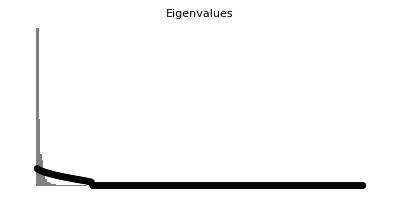
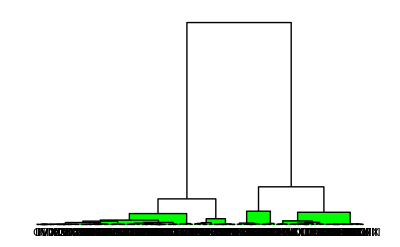
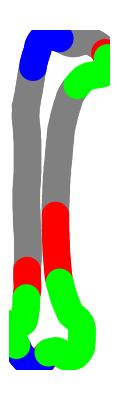
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 19.3924 |  | 
Relative Eigenvalue SD: 3.32577 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
(*brokeoutlines[[7]]*)
```

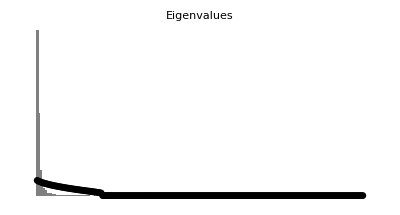
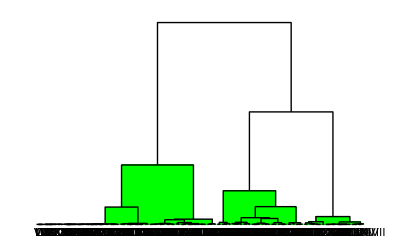
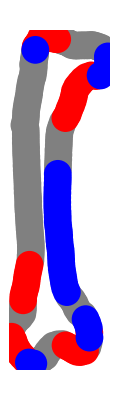
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 19.0734 |  | 
Relative Eigenvalue SD: 3.01577 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.156174 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

## HUMERUS

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Humerus/FL only/Humerus FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Humerus/F only/Humerus F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[HumerusLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=HumerusLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
HumerusProc1=Procrustes[means3, 200, 2];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[HumerusProc];
resids=#-Consensus&/@HumerusProc;
P=Covariance[HumerusProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
Fpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@F]];
FLpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@FL]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlyingTree,Transpose[{Union[shortlabels][[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
(*FlyingHumerusProc=FlyingICproc;*)
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlightlessTree,Transpose[{Union[shortlabels][[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
(*FlightlessHumerusProc=FlightlessICproc;*)
```

### Making covariance matrices:

```mathematica
FLCovIC=Covariance[FlightlessICproc];
FCovIC=Covariance[FlyingICproc];
```

## Mantel Test

```mathematica
(*Timing[MantelForMorphometrics[FLCovIC,FCovIC,10000]]
Speak["Mantel for humerus is finished"]*)
```

{362.08,{0.397549,0.}}

{362.08,{0.397549,0.}}

## CPCA

```mathematica
Labels=Join[ConstantArray["flying",Length[FlyingICproc]],ConstantArray["flightless",Length[FlightlessICproc]]];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICHumerusAllTaxa_NoGeneric_Scores.csv",Join[FlyingICscores,FlightlessICscores]*1000,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICHumerusAllTaxa_NoGeneric_labels.csv",Labels,"CSV"];
```

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaHumerus_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaHumerus_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaHumerus_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Humerusexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flightless | 23.3578 | 63.0676 | 2.58629 | 8.2769 | 0.220417 | 0.182828 | 0.475589 | 0.296878 | 0.180815 | 0.892553
flying | 58.3026 | 5.00521 | 7.53142 | 3.74764 | 11.3757 | 5.12322 | 0.583425 | 0.708813 | 0.966966 | 0.132027)

```mathematica
Humeruslambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Humerusloadings=icCPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*x=1;
Humeruscpc2=Table[
Test=(vectors[[1;;,1;;Length[icCPCAloadings]-1]].icCPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

### CPCA EV Comparison

```mathematica
X=1;
fEV=Table[Variance[Transpose[FlyingICscores][[X]]],{X,Length[Transpose[FlyingICscores]]}];
```

```mathematica
X=1;
flEV=Table[Variance[Transpose[FlightlessICscores][[X]]],{X,Length[Transpose[FlightlessICscores]]}];
```

```mathematica
HumerusICcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],AccountingForm[fEV[[1;;10]]],AccountingForm[CPCAlambda[[3,2;;11]],11],AccountingForm[flEV[[1;;10]]]};
HumerusICcpcaEV
```

{{0.000255389,0.000689569,0.000028278,0.000090498,0.00000241,0.000001999,0.0000052,0.000003246,0.000001977,0.000009759},{0.0000792471,0.0000126726,0.00000744276,0.000015574,0.00000563213,0.00000415267,0.00000186094,0.00000348685,0.00000171809,0.00000165959},{0.000079046,0.000006786,0.000010211,0.000005081,0.000015423,0.000006946,0.000000791,0.000000961,0.000001311,0.000000179},{0.000332917,0.0000389939,0.000211491,0.000061542,0.000254557,0.0000169913,0.0000270732,0.00000952284,0.0000638045,0.0000251813}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

1.04516

```mathematica
VectorAngle[CPCAlambda[[3,2;;6]],flEV[[1;;5]]]
```

0.55382

```mathematica
VectorAngle[CPCAlambda[[2,2;;3]],fEV[[1;;2]]]
```

1.05753

```mathematica
VectorAngle[CPCAlambda[[3,2;;3]],flEV[[1;;2]]]
```

0.0309578

## Eigenvalue Dispersion

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingICproc,200,2,Labels,"RandomizationTest"];
HuFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessICproc,200,2,Labels,"RandomizationTest"];
HuFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
HumerusED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*HumerusED//MatrixForm*)
```

```mathematica
(*brokeoutlines[[17]]*)
```

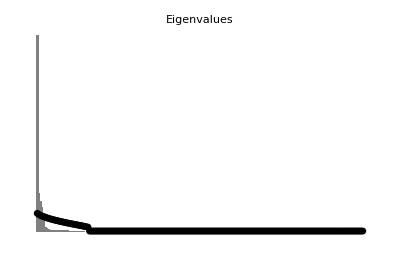
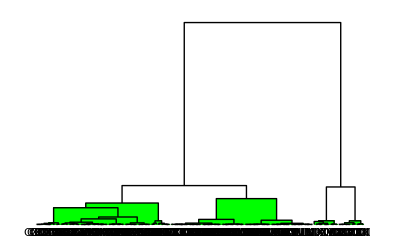
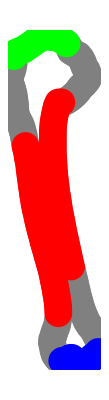
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 23.2258 |  | 
Relative Eigenvalue SD: 4.10578 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
(*brokeoutlines[[61]]*)
```

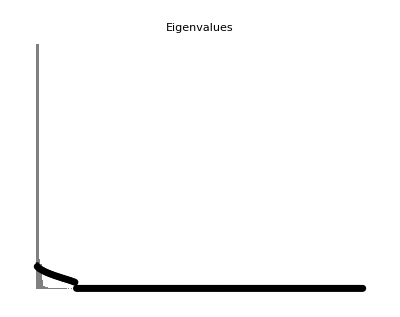
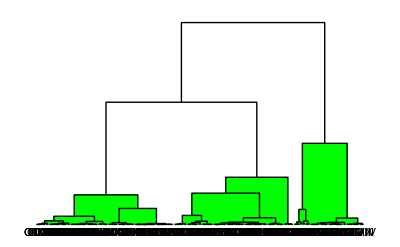
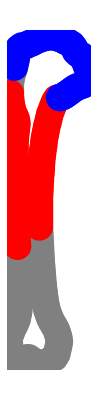
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 32.5991 |  | 
Relative Eigenvalue SD: 6.65426 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.2 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

## ULNA

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Ulna/FL only/Ulna FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Ulna/F only/Ulna F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
UlnaProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[UlnaLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=UlnaLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
UlnaProc1=Procrustes[means3, 200, 2];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[UlnaProc];
resids=#-Consensus&/@UlnaProc;
P=Covariance[UlnaProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
Fpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@F]];
FLpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@FL]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlyingTree,Transpose[{Union[shortlabels][[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
(*FlyingUlnaProc=FlyingICproc;*)
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlightlessTree,Transpose[{Union[shortlabels][[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
(*FlightlessUlnaProc=FlightlessICproc;*)
```

### Making covariance matrices:

```mathematica
FLCovIC=Covariance[FlightlessICproc];
FCovIC=Covariance[FlyingICproc];
```

## Mantel Test

```mathematica
(*Timing[MantelForMorphometrics[FLCovIC,FCovIC,10000]]
Speak["Mantel for ulna is finished"]*)
```

{330.928,{0.503092,0.}}

{330.928,{0.503092,0.}}

## CPCA

```mathematica
Labels=Join[ConstantArray["flying",Length[FlyingICproc]],ConstantArray["flightless",Length[FlightlessICproc]]];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICUlnaAllTaxa_NoGeneric_Scores.csv",Join[FlyingICscores,FlightlessICscores]*1000,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICUlnaAllTaxa_NoGeneric_labels.csv",Labels,"CSV"];
```

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaUlna_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaUlna_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaUlna_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Ulnaexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flightless | 75.605 | 15.7679 | 3.74966 | 1.34007 | 1.49072 | 0.759151 | 0.265352 | 0.129712 | 0.148467 | 0.0842157
flying | 20.126 | 44.7685 | 9.21627 | 9.41016 | 0.862747 | 2.17021 | 2.0279 | 1.72016 | 3.22151 | 0.633274)

```mathematica
Ulnalambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Ulnaloadings=icCPCAloadings[[1;;10,1;;10]]//MatrixForm;*)
```

```mathematica
(*x=1;
Ulnacpc1=Table[
Test=(vectors[[1;;,1;;Length[icCPCAloadings]-1]].icCPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

### CPCA EV Comparison

```mathematica
X=1;
fEV=Table[Variance[Transpose[FlyingICscores][[X]]],{X,Length[Transpose[FlyingICscores]]}];
```

```mathematica
X=1;
flEV=Table[Variance[Transpose[FlightlessICscores][[X]]],{X,Length[Transpose[FlightlessICscores]]}];
```

```mathematica
UlnaICcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],AccountingForm[fEV[[1;;10]]],AccountingForm[CPCAlambda[[3,2;;11]],11],AccountingForm[flEV[[1;;10]]]};
UlnaICcpcaEV
```

{{0.000624837,0.000130314,0.000030989,0.000011075,0.00001232,0.000006274,0.000002193,0.000001072,0.000001227,0.000000696},{0.000024714,0.0000106314,0.00000886609,0.00000382525,0.00000168029,0.00000155911,0.00000129674,0.000000976875,0.000000813608,0.000000644096},{0.000011314,0.000025167,0.000005181,0.00000529,0.000000485,0.00000122,0.00000114,0.000000967,0.000001811,0.000000356},{0.000248495,0.000123191,0.000340176,0.0000179437,0.0000142447,0.00000653499,0.0000460061,0.00000182628,0.0000216911,0.00000523386}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.35454

```mathematica
VectorAngle[CPCAlambda[[3,2;;6]],flEV[[1;;5]]]
```

0.903078

```mathematica
VectorAngle[CPCAlambda[[2,2;;3]],fEV[[1;;2]]]
```

0.200639

```mathematica
VectorAngle[CPCAlambda[[3,2;;3]],flEV[[1;;2]]]
```

0.688069

## Eigenvalue Dispersion

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingICproc,200,2,Labels,"RandomizationTest"];
UlFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessICproc,200,2,Labels,"RandomizationTest"];
UlFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
UlnaED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*UlnaED//MatrixForm*)
```

```mathematica
(*brokeoutlines[[10]]*)
```

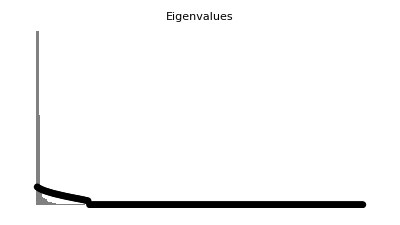
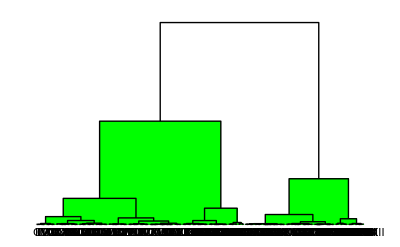
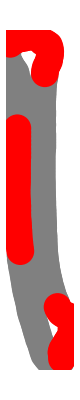
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 22.4303 |  | 
Relative Eigenvalue SD: 3.96515 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
(*brokeoutlines[[6]]*)
```

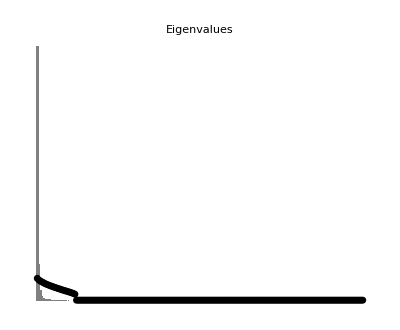
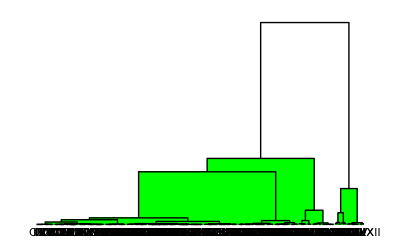
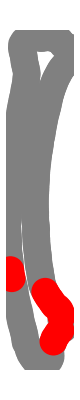
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 33.9751 |  | 
Relative Eigenvalue SD: 6.93513 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.2 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

## MANUS

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Manus/FL only/Manus FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Manus/F only/Manus F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
ManusData=ManusData[[1;;,1;;]];
labels=ManusData[[1;;,1]];
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
Union[StringSplit[#,"_"][[1]]&/@labels];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means1=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means1, 200, 2];
```

```mathematica
shortPos=Flatten[Position[ManusLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=ManusLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
ManusProc1=Procrustes[means3, 200, 2];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[ManusProc];
resids=#-Consensus&/@ManusProc;
P=Covariance[ManusProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
Fpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@F]];
FLpos=Sort[Flatten[Flatten[Position[Union[shortlabels],#]]&/@FL]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlyingTree,Transpose[{Union[shortlabels][[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
(*FlyingManusProc=FlyingICproc;*)
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FlightlessTree,Transpose[{Union[shortlabels][[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
(*FlightlessManusProc=FlightlessICproc;*)
```

### Making covariance matrices:

```mathematica
FLCovIC=Covariance[FlightlessICproc];
FCovIC=Covariance[FlyingICproc];
```

## Mantel Test

```mathematica
(*Timing[MantelForMorphometrics[FLCovIC,FCovIC,10000]]
Speak["Mantel for tarso is finished"]*)
```

{345.509,{0.458333,0.}}

{345.509,{0.458333,0.}}

## CPCA

```mathematica
Labels=Join[ConstantArray["flying",Length[FlyingICproc]],ConstantArray["flightless",Length[FlightlessICproc]]];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICManusAllTaxa_NoGeneric_Scores.csv",Join[FlyingICscores,FlightlessICscores]*1000,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICManusAllTaxa_NoGeneric_labels.csv",Labels,"CSV"];
```

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaManus_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaManus_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ICcpcaManus_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Manusexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flightless | 53.6097 | 13.5175 | 3.22015 | 1.66992 | 19.3336 | 4.28087 | 0.633257 | 1.59288 | 0.441848 | 0.064344
flying | 19.5684 | 43.7198 | 11.1413 | 6.95362 | 0.470432 | 2.80106 | 3.28664 | 0.405847 | 1.57555 | 1.36744)

```mathematica
Manuslambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Manusloadings=icCPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*x=1;
Manuscpc1=Table[
Test=(vectors[[1;;,1;;Length[icCPCAloadings]-1]].icCPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]*)
```

### CPCA EV Comparison

```mathematica
X=1;
fEV=Table[Variance[Transpose[FlyingICscores][[X]]],{X,Length[Transpose[FlyingICscores]]}];
```

```mathematica
X=1;
flEV=Table[Variance[Transpose[FlightlessICscores][[X]]],{X,Length[Transpose[FlightlessICscores]]}];
```

```mathematica
ManusICcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],AccountingForm[fEV[[1;;10]]],AccountingForm[CPCAlambda[[3,2;;11]],11],AccountingForm[flEV[[1;;10]]]};
ManusICcpcaEV
```

{{0.000726527,0.000183192,0.00004364,0.000022631,0.000262012,0.000058015,0.000008582,0.000021587,0.000005988,0.000000872},{0.0000432284,0.0000341475,0.0000149195,0.00000953566,0.00000412145,0.00000275724,0.00000380818,0.00000264966,0.00000336966,0.00000103215},{0.000024542,0.000054832,0.000013973,0.000008721,0.00000059,0.000003513,0.000004122,0.000000509,0.000001976,0.000001715},{0.000417276,0.000291308,0.0000326507,0.000146406,0.0000765803,0.000101765,0.0000100502,0.0000259463,0.0000432948,0.0000132263}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.538365

```mathematica
VectorAngle[CPCAlambda[[3,2;;6]],flEV[[1;;5]]]
```

0.576679

```mathematica
VectorAngle[CPCAlambda[[2,2;;3]],fEV[[1;;2]]]
```

0.421574

```mathematica
VectorAngle[CPCAlambda[[3,2;;3]],flEV[[1;;2]]]
```

0.54049

## Eigenvalue Dispersion

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingICproc,200,2,Labels,"RandomizationTest"];
MaFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessICproc,200,2,Labels,"RandomizationTest"];
MaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
ManusED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*ManusED//MatrixForm*)
```

```mathematica
(*brokeoutlines[[79]]*)
```

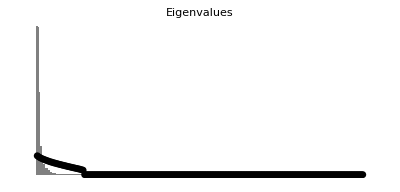
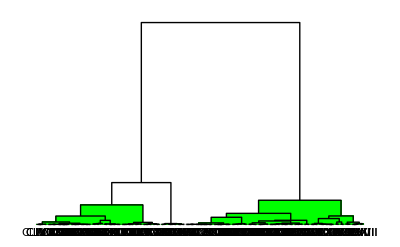
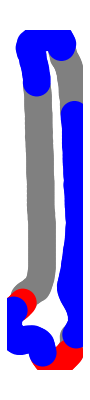
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 20.7483 |  | 
Relative Eigenvalue SD: 3.85286 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
(*brokeoutlines[[6]]*)
```

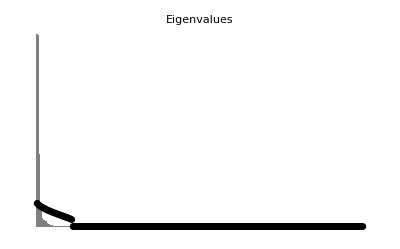
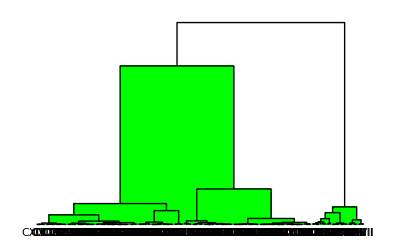
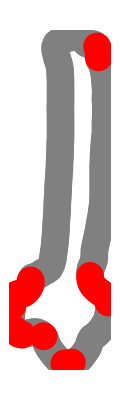
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 28.3365 |  | 
Relative Eigenvalue SD: 6.04136 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.208514 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

## EV Dispersion Results

```mathematica
EVDispersionResults={HuFMod,HuFLMod,UlFMod,UlFLMod,MaFMod,MaFLMod,FeFMod,FeFLMod,TiFMod,TiFLMod,TaFMod,TaFLMod};
```

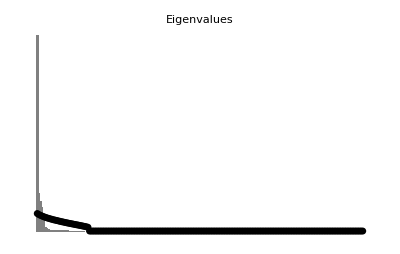
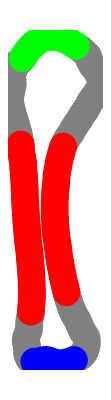
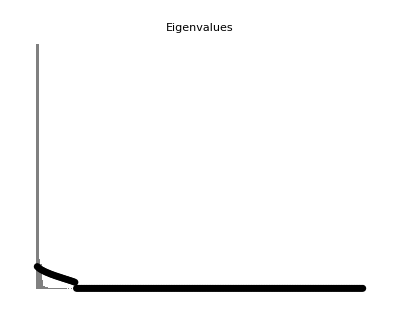
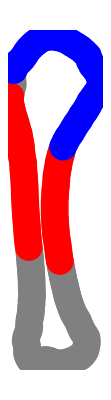
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 23.2258 |  | 
Relative Eigenvalue SD: 4.10578 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 32.5991 |  | 
Relative Eigenvalue SD: 6.65426 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.2 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{HuFMod,HuFLMod}
```

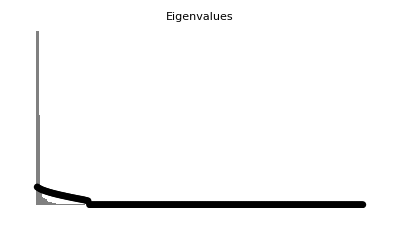
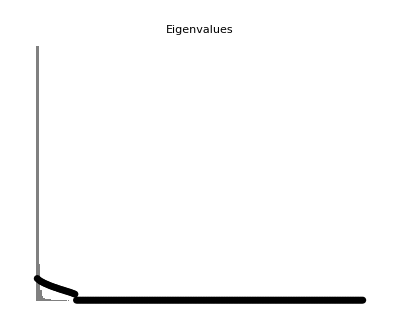
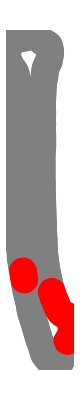
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 22.4303 |  | 
Relative Eigenvalue SD: 3.96515 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 33.9751 |  | 
Relative Eigenvalue SD: 6.93513 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.2 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{UlFMod,UlFLMod}
```

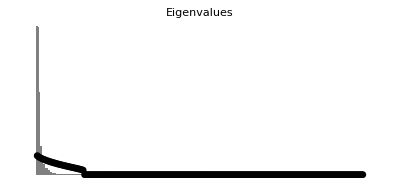
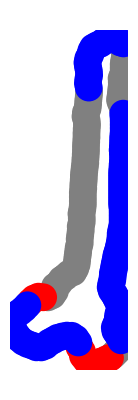
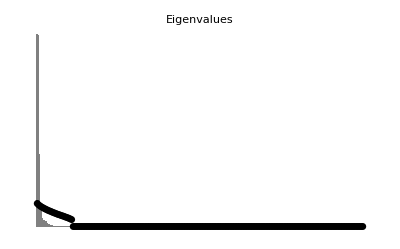
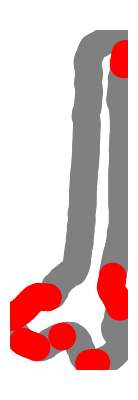
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 20.7483 |  | 
Relative Eigenvalue SD: 3.85286 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 28.3365 |  | 
Relative Eigenvalue SD: 6.04136 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.208514 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{MaFMod,MaFLMod}
```

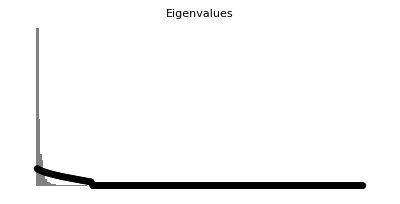
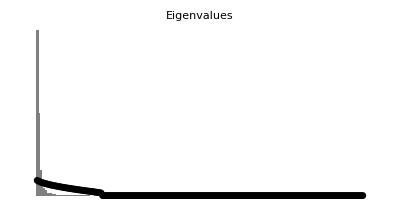
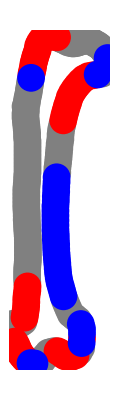
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 19.3924 |  | 
Relative Eigenvalue SD: 3.32577 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 19.0734 |  | 
Relative Eigenvalue SD: 3.01577 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.156174 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{FeFMod,FeFLMod}
```

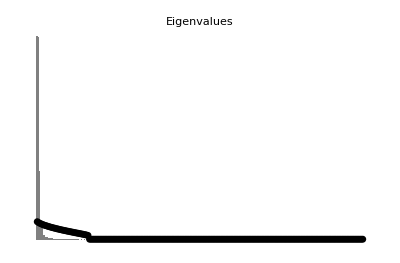
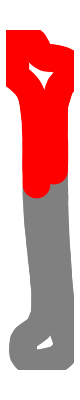
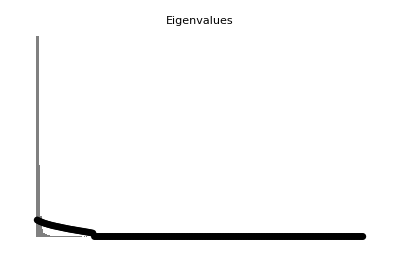
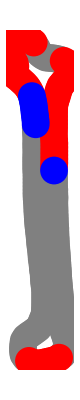
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 24.5723 |  | 
Relative Eigenvalue SD: 4.34382 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 23.3586 |  | 
Relative Eigenvalue SD: 3.94832 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.166667 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{TiFMod,TiFLMod}
```

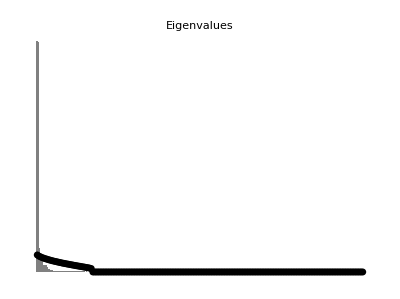
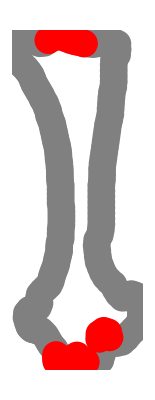
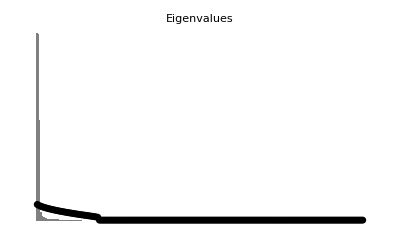
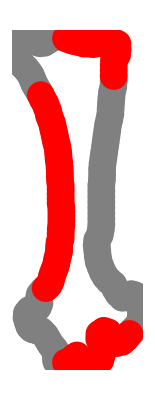
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 25.7902 |  | 
Relative Eigenvalue SD: 4.42298 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 22.228 |  | 
Relative Eigenvalue SD: 3.60586 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.160128 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{TaFMod,TaFLMod}
```

```mathematica
EVDispersionResultsNumbsOnly=Partition[Flatten[Join[{HumerusED,UlnaED,ManusED,FemurED,TibiaED,TarsoED}]],5]//MatrixForm
```

(  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
Flying |  23.2258 |  4.10578 |  0.174078 |  4
Flightless |  32.5991 |  6.65426 |  0.2 |  3
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
Flying |  22.4303 |  3.96515 |  0.174078 |  2
Flightless |  33.9751 |  6.93513 |  0.2 |  2
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
Flying |  20.7483 |  3.85286 |  0.182574 |  3
Flightless |  28.3365 |  6.04136 |  0.208514 |  2
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
Flying |  19.3924 |  3.32577 |  0.169031 |  4
Flightless |  19.0734 |  3.01577 |  0.156174 |  3
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
Flying |  24.5723 |  4.34382 |  0.174078 |  2
Flightless |  23.3586 |  3.94832 |  0.166667 |  3
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
Flying |  25.7902 |  4.42298 |  0.169031 |  2
Flightless |  22.228 |  3.60586 |  0.160128 |  2)

## CPCA - EV Comparison Results

```mathematica
{Humerusexpvar,HumerusICcpcaEV,Ulnaexpvar,UlnaICcpcaEV,Manusexpvar,ManusICcpcaEV,Femurexpvar,FemurICcpcaEV,Tibiaexpvar,TibiaICcpcaEV,Tarsoexpvar,TarsoICcpcaEV};
```

```mathematica
AllTaxaICcpcaEVResults={HumerusICcpcaEV,UlnaICcpcaEV,ManusICcpcaEV,FemurICcpcaEV,TibiaICcpcaEV,TarsoICcpcaEV};
```

```mathematica
HumerusICcpcaEV
```

{{0.000255389,0.000689569,0.000028278,0.000090498,0.00000241,0.000001999,0.0000052,0.000003246,0.000001977,0.000009759},{0.0000792471,0.0000126726,0.00000744276,0.000015574,0.00000563213,0.00000415267,0.00000186094,0.00000348685,0.00000171809,0.00000165959},{0.000079046,0.000006786,0.000010211,0.000005081,0.000015423,0.000006946,0.000000791,0.000000961,0.000001311,0.000000179},{0.000332917,0.0000389939,0.000211491,0.000061542,0.000254557,0.0000169913,0.0000270732,0.00000952284,0.0000638045,0.0000251813}}

```mathematica
UlnaICcpcaEV
```

{{0.000624837,0.000130314,0.000030989,0.000011075,0.00001232,0.000006274,0.000002193,0.000001072,0.000001227,0.000000696},{0.000024714,0.0000106314,0.00000886609,0.00000382525,0.00000168029,0.00000155911,0.00000129674,0.000000976875,0.000000813608,0.000000644096},{0.000011314,0.000025167,0.000005181,0.00000529,0.000000485,0.00000122,0.00000114,0.000000967,0.000001811,0.000000356},{0.000248495,0.000123191,0.000340176,0.0000179437,0.0000142447,0.00000653499,0.0000460061,0.00000182628,0.0000216911,0.00000523386}}

```mathematica
ManusICcpcaEV
```

{{0.000726527,0.000183192,0.00004364,0.000022631,0.000262012,0.000058015,0.000008582,0.000021587,0.000005988,0.000000872},{0.0000432284,0.0000341475,0.0000149195,0.00000953566,0.00000412145,0.00000275724,0.00000380818,0.00000264966,0.00000336966,0.00000103215},{0.000024542,0.000054832,0.000013973,0.000008721,0.00000059,0.000003513,0.000004122,0.000000509,0.000001976,0.000001715},{0.000417276,0.000291308,0.0000326507,0.000146406,0.0000765803,0.000101765,0.0000100502,0.0000259463,0.0000432948,0.0000132263}}

```mathematica
FemurICcpcaEV
```

{{0.00030411,0.000154033,0.000026949,0.000011977,0.000006178,0.000046426,0.000007775,0.000013077,0.000006292,0.000001087},{0.0000340173,0.0000303593,0.000016079,0.0000129957,0.00000903293,0.00000305242,0.00000152586,0.00000207419,0.00000118339,0.0000005713},{0.000046678,0.000026109,0.000009621,0.000014168,0.000006641,0.000001141,0.000001946,0.000000831,0.000000885,0.000002554},{0.000201951,0.000207331,0.0000794241,0.0000158529,0.00000920369,0.00000939477,0.000011313,0.00000704011,0.00000357801,0.00000410537}}

```mathematica
TibiaICcpcaEV
```

{{0.000142717,0.000029396,0.000220485,0.000016807,0.000007039,0.000001213,0.000004691,0.000005739,0.000000897,0.000002562},{0.0000322188,0.000015977,0.00000516339,0.00000292702,0.00000183651,0.00000310961,0.000000888691,0.00000137657,0.000000880662,0.000000449155},{0.000031988,0.000018194,0.000001142,0.000003605,0.000002905,0.000002852,0.000000979,0.00000026,0.000000886,0.00000028},{0.000112008,0.0000261366,0.000165708,0.0000443966,0.00000851462,0.0000153313,0.0000219346,0.00000200017,0.0000108638,0.00000826725}}

```mathematica
TarsoICcpcaEV
```

{{0.000227024,0.000758473,0.000045276,0.000016578,0.00001049,0.000006089,0.000027582,0.000002028,0.000000926,0.000000656},{0.000193148,0.0000307253,0.0000105285,0.0000121024,0.00000869141,0.00000688328,0.00000798334,0.00000483829,0.00000269958,0.00000263424},{0.000200212,0.000006073,0.000024394,0.0000097,0.000008463,0.000013728,0.000003154,0.000002239,0.000006802,0.000004459},{0.000242398,0.000234942,0.000161263,0.0000177706,0.0000151197,0.0000910441,0.00016075,0.0000150942,0.0000506829,0.00000835872}}

```mathematica
AllTaxaICcpcaResults={{Humerusexpvar,Humeruslambda,Humerusloadings,Humeruscpc2,HumerusICcpcaEV},{Ulnaexpvar,Ulnalambda,Ulnaloadings,Ulnacpc1,UlnaICcpcaEV},{Manusexpvar,Manuslambda,Manusloadings,Manuscpc1,ManusICcpcaEV},{Femurexpvar,Femurlambda,Femurloadings,FemurICcpcaEV},{Tibiaexpvar,Tibialambda,Tibialoadings,TibiaICcpcaEV},{Tarsoexpvar,Tarsolambda,Tarsoloadings,Tarsocpc1,Tarsocpc2,TarsoICcpcaEV}};
```

# Whole Limb Eigenvalue Dispersion

## Intro

```mathematica
<<PollyMorphometrics`
<<PollyPhylogenetics`
<<PollyModularity`
```

PollyMorphometrics 12.2
(c) P. David Polly, 5 March 2017

Phylogenetics for Mathematica 5.0
(c) P. David Polly, 21 January 2018

Modularity for Mathematica 2.0
(c) P. David Polly and A. Goswami, 20 Dec 2010
Updated 7 April 2018.

```mathematica
<<HierarchicalClustering`
Modularity[Landmarks_,NLands_,NDims_,Labels_,Randomization_:"False"]:=Module[{superimposed,residuals,P2,EVStdev2,Plot2,NinetyFivePercentCutoff2,Tree2,EV2,BootEV2,MaxMinBootEV2,MeanBootEV1,MeanBootEV2,
Rows,Columns,dims,NumMods2,RelEVStdev2,ModulePicture},
superimposed=Landmarks;
superimposed=Partition[Partition[Flatten[superimposed],NDims],NLands];
{Rows,Columns,dims}=Dimensions[superimposed];
P2=CanonicalCorrelation[superimposed];
EV2=Chop[Eigenvalues[P2]];
EVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]];
RelEVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]]/Sqrt[MatrixRank[P2]];


If[Randomization=="RandomizationTest",
BootEV2=Table[Eigenvalues[CanonicalCorrelation[Partition[superimposed[[#[[1]],#[[2]]]]&/@Flatten[ Table[Table[{RandomInteger[{1,Rows}],RandomInteger[{1,Columns}]},{Columns}],{Rows}],1],NLands]]
]
,{100}];
MaxMinBootEV2=Chop[Transpose[{Max[#]&/@Transpose[BootEV2],Min[#]&/@Transpose[BootEV2]}]];
MeanBootEV2=Chop[Mean[#]&/@Transpose[BootEV2]];
NumMods2=Length[Select[EV2-(#[[1]]&/@MaxMinBootEV2),Positive]];
If[NumMods2==0,NumMods2=1];
Plot2=Graphics[{
{Gray,Table[Rectangle[{x-.45,0},{x+.45,EV2[[x]]}],{x,Length[EV2]}]},
{Black,AbsoluteThickness[2],Dashed,Table[Line[{{x,MaxMinBootEV2[[x,2]]},{x,MaxMinBootEV2[[x,1]]}}],{x,Length[MaxMinBootEV2]}]},
{Black,AbsolutePointSize[5],Table[Point[{x,MeanBootEV2[[x]]}],{x,Length[MeanBootEV2]}]}
},PlotLabel->"Eigenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&),HighlightLevel->NumMods2];

clust=Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"];
If[NumMods2>1,splitClusts=ClusterSplit[clust,NumMods2]];

If[NumMods2<2,
AllComas=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[clust],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[1<NumMods2<3,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[2<NumMods2<4,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[3<NumMods2<5,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];
If[4<NumMods2<6,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas5=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[5]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];
If[5<NumMods2<7,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas5=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[5]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas6=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[6]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[NumMods2<2,TipPos=Flatten[Position[AllComas,#]&/@Labels];
Tips=FromRomanNumeral[AllComas[[Sort[TipPos]]]];];

If[1<NumMods2<3,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
AllTips={Tips1,Tips2};
CorrectTips=AllTips;];

If[2<NumMods2<4,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
AllTips={Tips1,Tips2,Tips3};
CorrectTips=AllTips;];

If[3<NumMods2<5,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
AllTips={Tips1,Tips2,Tips3,Tips4};
CorrectTips=AllTips;];

If[4<NumMods2<6,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
TipPos5=Flatten[Position[AllComas5,#]&/@Labels];
Tips5=FromRomanNumeral[AllComas5[[Sort[TipPos5]]]];
AllTips={Tips1,Tips2,Tips3,Tips4,Tips5};
CorrectTips=AllTips;];

If[5<NumMods2<7,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
TipPos5=Flatten[Position[AllComas5,#]&/@Labels];
Tips5=FromRomanNumeral[AllComas5[[Sort[TipPos5]]]];
TipPos6=Flatten[Position[AllComas6,#]&/@Labels];
Tips6=FromRomanNumeral[AllComas6[[Sort[TipPos6]]]];
AllTips={Tips1,Tips2,Tips3,Tips4,Tips5,Tips6};
CorrectTips=AllTips;];

If[NumMods2<2,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[Tips]]]}
}
]];
If[1<NumMods2<3,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]}
}
];];
If[2<NumMods2<4,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]}
}
];];
If[3<NumMods2<5,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]}
}
];];
If[4<NumMods2<6,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]},
{Purple,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[5]]]]]}
}
];];
If[5<NumMods2<7,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]},
{Purple,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[5]]]]]},
{Yellow,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[6]]]]]}
}
];];

Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eignvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{"Estimated Number of Modules: "<>ToString[NumMods2]},
(*{Plot2,Tree2,ModulePicture},*)
{Plot2,Tree2,ModulePicture}
},Alignment->Left],FontFamily->"Helvetica"]
]
,

Plot2=BarChart[EV2,PlotLabel->"Eigvenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&)];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eigenvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{Plot2,Tree2}
},Alignment->Left],FontFamily->"Helvetica"]
]
];
]
```

```mathematica
(*HindLimbMissingList={"AmericanCoot","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","DblCrstdCormorant","FlyingSD","Gull","Hoatzin","HornedGrebe","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RedLggdSeriema","RockPigeon","RuffedGrouse","ShrtTldShearwater","Sora","StripedManakin","YllwCrwndAmazon","A.otidiformis","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GiantCoot","GuamRail","JuninGrebe","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","TasNativehen","TiticacaGrebe","TristanMoorhen","Weka"};*)
```

```mathematica
(*ForeLimbMissingList={"ChubutSD","FalklandSD","FlgtlessCormorant","FuegianSD","GiantCoot","GuamRail","JuninGrebe","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.lemoinei","TasNativehen","TiticacaGrebe","TristanMoorhen","Weka","AmericanCoot","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","DblCrstdCormorant","FlyingSD","Gull","Hoatzin","HornedGrebe","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RedLggdSeriema","RockPigeon","RuffedGrouse","ShrtTldShearwater","Sora","StripedManakin","YllwCrwndAmazon"};*)
```

## Hind Limb

## Intro

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
AllTaxa={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
```

TARSOMETATARSUS

## Intro

```mathematica
FHindLimbTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/F Hind Limb EVD no auks"];
FLHindLimbTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/FL Hind Limb EVD no auks"];
```

### Scores of TarsoProc:

```mathematica
Consensus=Mean[TarsoProc1];
resids=#-Consensus&/@TarsoProc1;
P=Covariance[TarsoProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TarsoProc (& also "scores"):

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
FLpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
Fpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
```

```mathematica
slabels=Union[StringSplit[#,"_"][[1]]&/@HLlist];
```

### Dividing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FHindLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingTarsoProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLHindLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessTarsoProc=FlightlessICproc;
```

TIBIOTARSUS

## Intro

### Scores of TibiaProc:

```mathematica
Consensus=Mean[TibioProc1];
resids=#-Consensus&/@TibioProc1;
P=Covariance[TibioProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FHindLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingTibioProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLHindLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessTibioProc=FlightlessICproc;
```

FEMUR

## Intro

### Scores of TibiaProc:

```mathematica
Consensus=Mean[FemurProc1];
resids=#-Consensus&/@FemurProc1;
P=Covariance[FemurProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FHindLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingFemurProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLHindLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessFemurProc=FlightlessICproc;
```

EV Disp

```mathematica
PartProc=Table[Partition[FlyingTibioProc[[X]],2],{X,Length[FlyingTibioProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlyingTibioProc2=PartProc;

PartProc=Table[Partition[FlyingFemurProc[[X]],2],{X,Length[FlyingFemurProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlyingFemurProc2=PartProc;

PartProc=Table[Partition[FlightlessTibioProc[[X]],2],{X,Length[FlightlessTibioProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlightlessTibioProc2=PartProc;

PartProc=Table[Partition[FlightlessFemurProc[[X]],2],{X,Length[FlightlessFemurProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlightlessFemurProc2=PartProc;
```

```mathematica
X=1;
FlyingTarsoTibioProc=Table[Flatten[Append[FlyingTarsoProc[[X]],FlyingTibioProc2[[X]]]],{X,Length[FlyingTarsoProc]}];
X=1;
FlyingHindLimbProc=Table[Flatten[Append[FlyingTarsoTibioProc[[X]]
,FlyingFemurProc2[[X]]]],{X,Length[FlyingTarsoTibioProc]}];
X=1;
FlightlessTarsoTibioProc=Table[Flatten[Append[FlightlessTarsoProc[[X]],FlightlessTibioProc2[[X]]]],{X,Length[FlightlessTarsoProc]}];
X=1;
FlightlessHindLimbProc=Table[Flatten[Append[FlightlessTarsoTibioProc[[X]]
,FlightlessFemurProc2[[X]]]],{X,Length[FlightlessTarsoTibioProc]}];
```

```mathematica
Labels=RomanNumeral[Range[1,600]];
```

```mathematica
brokeoutlines=FlyingHindLimbProc;
FMod=Modularity[FlyingHindLimbProc,600,2,Labels,"RandomizationTest"];
HindLimbFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
brokeoutlines=FlightlessHindLimbProc;
FLMod=Modularity[FlightlessHindLimbProc,600,2,Labels,"RandomizationTest"];
HindLimbFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
HindLimbED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*HindLimbED//MatrixForm*)
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

EV Disp*

```mathematica
X=1;
PartFlyingTibioProc=Table[Partition[FlyingTibioProc[[X]],2],{X,Length[FlyingTibioProc]}];
M=1;
FlyingTibioProc2=Table[
Riffle[Table[PartFlyingTibioProc[[M,X,1]]*-1,{X,Length[PartFlyingTibioProc[[1]]]}],PartFlyingTibioProc[[M,1;;,2]]]
,{M,Length[PartFlyingTibioProc]}];

X=1;
PartFlyingTibioProc=Table[Partition[FlyingTibioProc2[[X]],2],{X,Length[FlyingTibioProc2]}];
M=1;
FlyingTibioProc2=Table[
Riffle[Table[PartFlyingTibioProc[[M,X,2]]*-1,{X,Length[PartFlyingTibioProc[[1]]]}],PartFlyingTibioProc[[M,1;;,1]]]
,{M,Length[PartFlyingTibioProc]}];

X=1;
PartFlightlessTibioProc=Table[Partition[FlightlessTibioProc[[X]],2],{X,Length[FlightlessTibioProc]}];
M=1;
FlightlessTibioProc2=Table[
Riffle[Table[PartFlightlessTibioProc[[M,X,1]]*-1,{X,Length[PartFlightlessTibioProc[[1]]]}],PartFlightlessTibioProc[[M,1;;,2]]]
,{M,Length[PartFlightlessTibioProc]}];

X=1;
PartFlightlessTibioProc=Table[Partition[FlightlessTibioProc2[[X]],2],{X,Length[FlightlessTibioProc2]}];
M=1;
FlightlessTibioProc2=Table[
Riffle[Table[PartFlightlessTibioProc[[M,X,2]]*-1,{X,Length[PartFlightlessTibioProc[[1]]]}],PartFlightlessTibioProc[[M,1;;,1]]]
,{M,Length[PartFlightlessTibioProc]}];
```

```mathematica
X=1;
PartFlyingFemurProc=Table[Partition[FlyingFemurProc[[X]],2],{X,Length[FlyingFemurProc]}];
M=1;
FlyingFemurProc2=Table[
Riffle[Table[PartFlyingFemurProc[[M,X,2]]*-1,{X,Length[PartFlyingFemurProc[[1]]]}],PartFlyingFemurProc[[M,1;;,1]]]
,{M,Length[PartFlyingFemurProc]}];

X=1;
PartFlightlessFemurProc=Table[Partition[FlightlessFemurProc[[X]],2],{X,Length[FlightlessFemurProc]}];
M=1;
FlightlessFemurProc2=Table[
Riffle[Table[PartFlightlessFemurProc[[M,X,2]]*-1,{X,Length[PartFlightlessFemurProc[[1]]]}],PartFlightlessFemurProc[[M,1;;,1]]]
,{M,Length[PartFlightlessFemurProc]}];
```

```mathematica
X=1;
PartFlightlessTarsoProc=Table[Partition[FlightlessTarsoProc[[X]],2],{X,Length[FlightlessTarsoProc]}];
M=1;
FlightlessTarsoProc2=Table[Riffle[PartFlightlessTarsoProc[[M,1;;,2]],Table[PartFlightlessTarsoProc[[M,X,1]]*-1,{X,Length[PartFlightlessTarsoProc[[1]]]}]]
,{M,Length[PartFlightlessTarsoProc]}];
X=1;
PartFlyingTarsoProc=Table[Partition[FlyingTarsoProc[[X]],2],{X,Length[FlyingTarsoProc]}];
M=1;
FlyingTarsoProc2=Table[
Riffle[PartFlyingTarsoProc[[M,1;;,2]],Table[PartFlyingTarsoProc[[M,X,1]]*-1,{X,Length[PartFlyingTarsoProc[[1]]]}]]
,{M,Length[PartFlyingTarsoProc]}];
```

```mathematica
PartProc=Table[Partition[FlyingTibioProc2[[X]],2],{X,Length[FlyingTibioProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlyingTibioProc2=PartProc;

PartProc=Table[Partition[FlyingFemurProc2[[X]],2],{X,Length[FlyingFemurProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlyingFemurProc2=PartProc;

PartProc=Table[Partition[FlightlessTibioProc2[[X]],2],{X,Length[FlightlessTibioProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlightlessTibioProc2=PartProc;

PartProc=Table[Partition[FlightlessFemurProc2[[X]],2],{X,Length[FlightlessFemurProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlightlessFemurProc2=PartProc;
```

```mathematica
X=1;
FlyingTarsoTibioProc=Table[Flatten[Append[FlyingTarsoProc2[[X]],FlyingTibioProc2[[X]]]],{X,Length[FlyingTarsoProc2]}];
X=1;
FlyingHindLimbProc=Table[Flatten[Append[FlyingTarsoTibioProc[[X]]
,FlyingFemurProc2[[X]]]],{X,Length[FlyingTarsoTibioProc]}];
X=1;
FlightlessTarsoTibioProc=Table[Flatten[Append[FlightlessTarsoProc2[[X]],FlightlessTibioProc2[[X]]]],{X,Length[FlightlessTarsoProc2]}];
X=1;
FlightlessHindLimbProc=Table[Flatten[Append[FlightlessTarsoTibioProc[[X]]
,FlightlessFemurProc2[[X]]]],{X,Length[FlightlessTarsoTibioProc]}];
```

```mathematica
Labels=RomanNumeral[Range[1,600]];
```

```mathematica
brokeoutlines=FlyingHindLimbProc;
```

```mathematica
FMod=Modularity[FlyingHindLimbProc,600,2,Labels,"RandomizationTest"];
HindLimbFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessHindLimbProc,600,2,Labels,"RandomizationTest"];
HindLimbFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Result

```mathematica
HindLimbED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*HindLimbED//MatrixForm*)
```

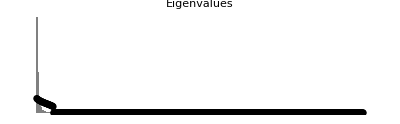
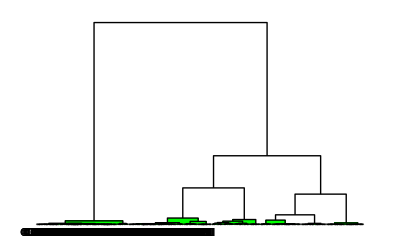
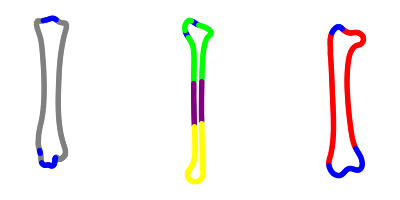
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 47.1906 |  | 
Relative Eigenvalue SD: 8.47568 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.176777 |  | 
Estimated Number of Modules: 6 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

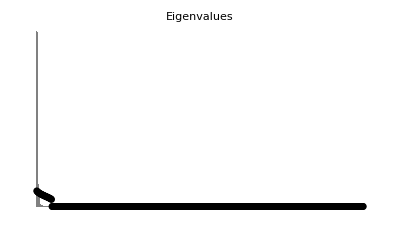
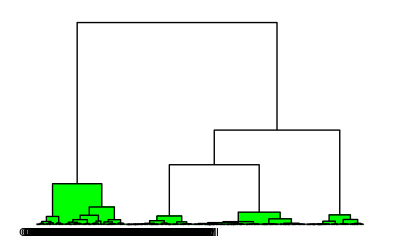
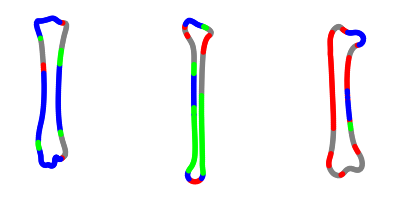
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 69.9025 |  | 
Relative Eigenvalue SD: 13.2103 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.185695 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

## Forelimb

## Intro

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
AllTaxa={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
```

```mathematica
FForeLimbTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/F Forelimb EVD no auks"];
FLForeLimbTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/FL Forelimb EVD no auks"];
```

HUMERUS

## Intro

### Scores of TibiaProc:

```mathematica
Consensus=Mean[HumerusProc1];
resids=#-Consensus&/@HumerusProc1;
P=Covariance[HumerusProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
FLpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
Fpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

```mathematica
slabels=Union[StringSplit[#,"_"][[1]]&/@ForLlist];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FForeLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingHumerusProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLForeLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessHumerusProc=FlightlessICproc;
```

HUMERUS - New

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Humerus/FL only/Humerus FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Humerus/F only/Humerus F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[HumerusLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=HumerusLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
HumerusProc1=Procrustes[means3, 200, 2];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[HumerusProc1];
resids=#-Consensus&/@HumerusProc1;
P=Covariance[HumerusProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
FLpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
Fpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

```mathematica
slabels=Union[StringSplit[#,"_"][[1]]&/@ForLlist];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FForeLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
FlyingHumerusProc=#+Consensus&/@ICresids;
(*ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingHumerusProc=FlyingICproc;*)
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLForeLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
FlightlessHumerusProc=#+Consensus&/@ICresids;
(*ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessHumerusProc=FlightlessICproc;*)
```

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingHumerusProc,200,2,Labels,"RandomizationTest"];
MaFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessHumerusProc,200,2,Labels,"RandomizationTest"];
MaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

### Mod

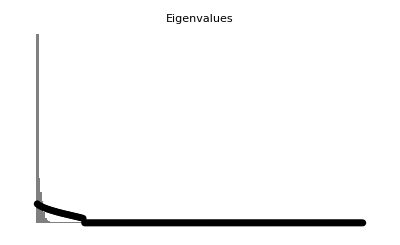
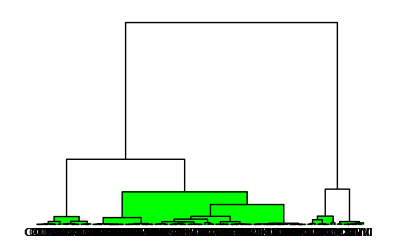
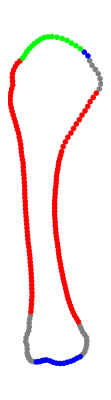
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 23.7871 |  | 
Relative Eigenvalue SD: 4.41715 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

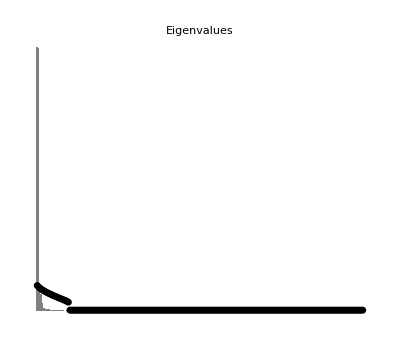
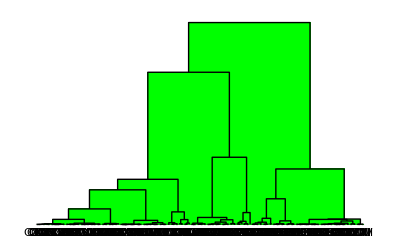
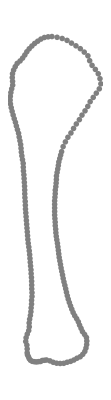
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 38.2677 |  | 
Relative Eigenvalue SD: 8.55692 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.218218 |  | 
Estimated Number of Modules: 1 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

ULNA - New

## Intro

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Ulna/FL only/Ulna FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Ulna/F only/Ulna F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
UlnaProc=Procrustes[means2, 200, 2];
```

```mathematica
shortPos=Flatten[Position[UlnaLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=UlnaLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
UlnaProc1=Procrustes[means3, 200, 2];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
FLpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
Fpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

```mathematica
slabels=Union[StringSplit[#,"_"][[1]]&/@ForLlist];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[UlnaProc1];
resids=#-Consensus&/@UlnaProc1;
P=Covariance[UlnaProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FForeLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
FlyingUlnaProc=#+Consensus&/@ICresids;
(*ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingUlnaProc=FlyingICproc;*)
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLForeLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
FlightlessUlnaProc=#+Consensus&/@ICresids;
(*ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessUlnaProc=FlightlessICproc;*)
```

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingUlnaProc,200,2,Labels,"RandomizationTest"];
MaFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessUlnaProc,200,2,Labels,"RandomizationTest"];
MaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

### Mod

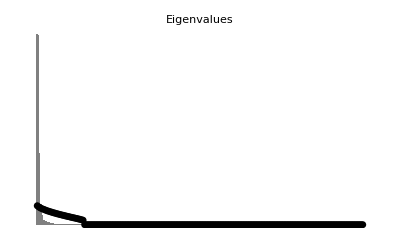
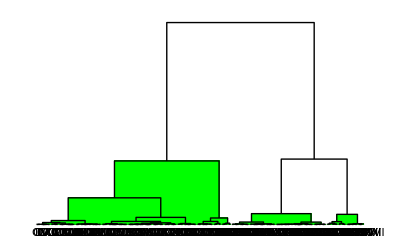
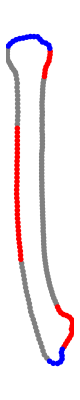
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 24.6018 |  | 
Relative Eigenvalue SD: 4.56845 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

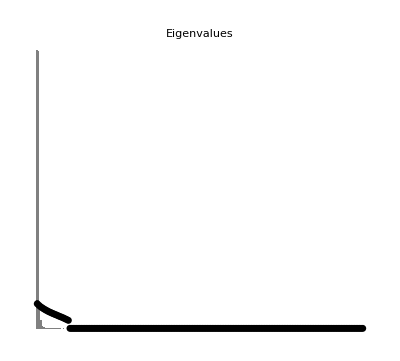
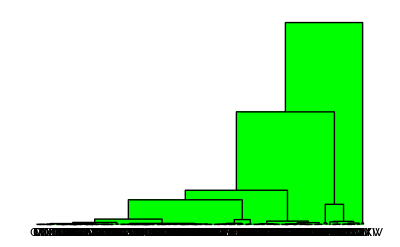
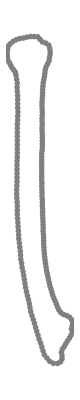
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 40.3939 |  | 
Relative Eigenvalue SD: 9.03235 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.218218 |  | 
Estimated Number of Modules: 1 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

ULNA

## Intro

### Scores of TibiaProc:

```mathematica
Consensus=Mean[UlnaProc1];
resids=#-Consensus&/@UlnaProc1;
P=Covariance[UlnaProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FForeLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingUlnaProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLForeLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessUlnaProc=FlightlessICproc;
```

MANUS - New

```mathematica
FlightlessTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Manus/FL only/Manus FL no auks"];
FlyingTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/Manus/F only/Manus F no auks"];
```

### Procrustes Superimpose the mean landmarks for each species:

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxa]]]];
ManusData=ManusData[[1;;,1;;]];
labels=ManusData[[1;;,1]];
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
Union[StringSplit[#,"_"][[1]]&/@labels];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means1=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means1, 200, 2];
```

```mathematica
shortPos=Flatten[Position[ManusLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=ManusLabels[[#]]&/@shortPos;
shortLabels1=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels1,#]]&/@Union[shortLabels1];
means3=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
ManusProc1=Procrustes[means3, 200, 2];
```

```mathematica
FForeLimbTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/F Forelimb EVD no auks"];
FLForeLimbTree=ReadNewick["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/Plot Trees/trees/MorphoJ trees/FL Forelimb EVD no auks"];
```

### Positions of flying (Fpos) and flightless (FLpos) species within TibiaProc (& also "scores"):

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
FLpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
Fpos=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

```mathematica
slabels=Union[StringSplit[#,"_"][[1]]&/@ForLlist];
```

### Scores of TibiaProc:

```mathematica
Consensus=Mean[ManusProc1];
resids=#-Consensus&/@ManusProc1;
P=Covariance[ManusProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FForeLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
FlyingManusProc=#+Consensus&/@ICresids;
(*ICproc=#+Consensus&/@ICresids;
FlyingManusProc=ICproc;
FlyingICproc=ICproc;*)
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLForeLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
FlightlessManusProc=#+Consensus&/@ICresids;
(*ICproc=#+Consensus&/@ICresids;
FlightlessManusProc=ICproc;
FlightlessICproc=ICproc;*)
```

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

```mathematica
FMod=Modularity[FlyingManusProc,200,2,Labels,"RandomizationTest"];
MaFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FlightlessManusProc,200,2,Labels,"RandomizationTest"];
MaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
ManusED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*ManusED//MatrixForm*)
```

### Mod

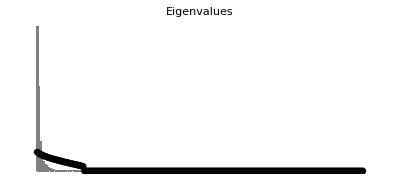
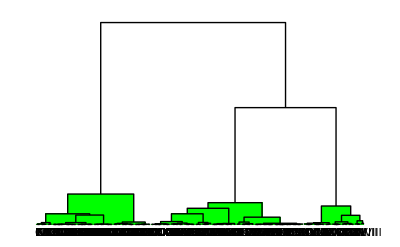
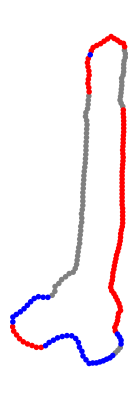
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 20.5572 |  | 
Relative Eigenvalue SD: 3.81738 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

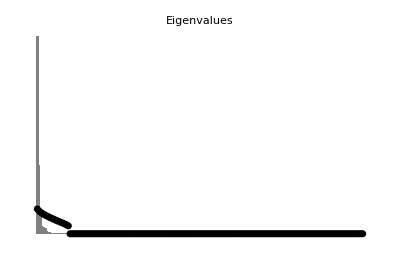
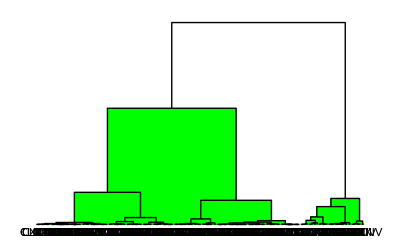
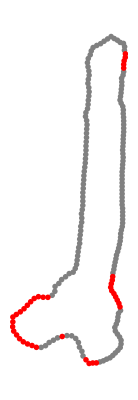
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 30.4145 |  | 
Relative Eigenvalue SD: 6.80089 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.218218 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

MANUS

## Intro

### Scores of TibiaProc:

```mathematica
Consensus=Mean[ManusProc1];
resids=#-Consensus&/@ManusProc1;
P=Covariance[ManusProc1];
{vectors,values, w}=SingularValueDecomposition[P];
scores=resids.vectors;
scores=scores[[1;;,1;;]];
```

### Diviing "scores" into Flying and Flightless scores

```mathematica
Fscores=scores[[Fpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FForeLimbTree,Transpose[{slabels[[Fpos]],Fscores[[1;;,X]]}]],{X,Length[Fscores[[1]]]}]];
FlyingICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlyingICproc=ICproc;
FlyingManusProc=FlyingICproc;
```

```mathematica
FLscores=scores[[FLpos]];
X=1;
ICscores=Transpose[Table[IndependentContrasts[FLForeLimbTree,Transpose[{slabels[[FLpos]],FLscores[[1;;,X]]}]],{X,Length[FLscores[[1]]]}]];
FlightlessICscores=ICscores;
ICresids=ICscores.Transpose[vectors];
ICproc=#+Consensus&/@ICresids;
FlightlessICproc=ICproc;
FlightlessManusProc=FlightlessICproc;
```

EV Disp

```mathematica
X=1;
PartFlyingUlnaProc=Table[Partition[FlyingUlnaProc[[X]],2],{X,Length[FlyingUlnaProc]}];
M=1;
FlyingUlnaProc2=Table[
Riffle[Table[PartFlyingUlnaProc[[M,X,2]]*-1,{X,Length[PartFlyingUlnaProc[[1]]]}],PartFlyingUlnaProc[[M,1;;,1]]]
,{M,Length[PartFlyingUlnaProc]}];

X=1;
PartFlightlessUlnaProc=Table[Partition[FlightlessUlnaProc[[X]],2],{X,Length[FlightlessUlnaProc]}];
M=1;
FlightlessUlnaProc2=Table[Riffle[Table[PartFlightlessUlnaProc[[M,X,2]]*-1,{X,Length[PartFlightlessUlnaProc[[1]]]}],PartFlightlessUlnaProc[[M,1;;,1]]]
,{M,Length[PartFlightlessUlnaProc]}];
```

```mathematica
X=1;
PartFlyingHumerusProc=Table[Partition[FlyingHumerusProc[[X]],2],{X,Length[FlyingHumerusProc]}];
M=1;
FlyingHumerusProc2=Table[Riffle[Table[PartFlyingHumerusProc[[M,X,1]]*-1,{X,Length[PartFlyingHumerusProc[[1]]]}],PartFlyingHumerusProc[[M,1;;,2]]],{M,Length[PartFlyingHumerusProc]}];

X=1;
FlyingHumerusProc2=Table[Partition[FlyingHumerusProc2[[X]],2],{X,Length[FlyingHumerusProc2]}];
M=1;
FlyingHumerusProc2=Table[Riffle[Table[FlyingHumerusProc2[[M,X,2]]*-1,{X,Length[FlyingHumerusProc2[[1]]]}],FlyingHumerusProc2[[M,1;;,1]]],{M,Length[FlyingHumerusProc2]}];

X=1;
PartFlightlessHumerusProc=Table[Partition[FlightlessHumerusProc[[X]],2],{X,Length[FlightlessHumerusProc]}];
M=1;
FlightlessHumerusProc2=Table[
Riffle[Table[PartFlightlessHumerusProc[[M,X,1]]*-1,{X,Length[PartFlightlessHumerusProc[[1]]]}],PartFlightlessHumerusProc[[M,1;;,2]]]
,{M,Length[PartFlightlessHumerusProc]}];

X=1;
FlightlessHumerusProc2=Table[Partition[FlightlessHumerusProc2[[X]],2],{X,Length[FlightlessHumerusProc2]}];
M=1;
FlightlessHumerusProc2=Table[
Riffle[Table[FlightlessHumerusProc2[[M,X,2]]*-1,{X,Length[FlightlessHumerusProc2[[1]]]}],FlightlessHumerusProc2[[M,1;;,1]]]
,{M,Length[FlightlessHumerusProc2]}];
```

```mathematica
X=1;
PartFlightlessManusProc=Table[Partition[FlightlessManusProc[[X]],2],{X,Length[FlightlessManusProc]}];
M=1;
FlightlessManusProc2=Table[Riffle[Table[PartFlightlessManusProc[[M,X,1]]*-1,{X,Length[PartFlightlessManusProc[[1]]]}],PartFlightlessManusProc[[M,1;;,2]]],{M,Length[PartFlightlessManusProc]}];

X=1;
PartFlightlessManusProc=Table[Partition[FlightlessManusProc2[[X]],2],{X,Length[FlightlessManusProc2]}];
M=1;
FlightlessManusProc2=Table[Riffle[Table[PartFlightlessManusProc[[M,X,2]]*-1,{X,Length[PartFlightlessManusProc[[1]]]}],PartFlightlessManusProc[[M,1;;,1]]],{M,Length[PartFlightlessManusProc]}];

X=1;
PartFlyingManusProc=Table[Partition[FlyingManusProc[[X]],2],{X,Length[FlyingManusProc]}];
M=1;
FlyingManusProc2=Table[Riffle[Table[PartFlyingManusProc[[M,X,1]]*-1,{X,Length[PartFlyingManusProc[[1]]]}],PartFlyingManusProc[[M,1;;,2]]],{M,Length[PartFlyingManusProc]}];

X=1;
PartFlyingManusProc=Table[Partition[FlyingManusProc2[[X]],2],{X,Length[FlyingManusProc2]}];
M=1;
FlyingManusProc2=Table[Riffle[Table[PartFlyingManusProc[[M,X,2]]*-1,{X,Length[PartFlyingManusProc[[1]]]}],PartFlyingManusProc[[M,1;;,1]]],{M,Length[PartFlyingManusProc]}];
```

```mathematica
PartProc=Table[Partition[FlyingHumerusProc2[[X]],2],{X,Length[FlyingHumerusProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlyingHumerusProc2=PartProc;

PartProc=Table[Partition[FlightlessHumerusProc2[[X]],2],{X,Length[FlightlessHumerusProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlightlessHumerusProc2=PartProc;
```

```mathematica
PartProc=Table[Partition[FlyingUlnaProc2[[X]],2],{X,Length[FlyingUlnaProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlyingUlnaProc2=PartProc;

PartProc=Table[Partition[FlightlessUlnaProc2[[X]],2],{X,Length[FlightlessUlnaProc2]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
FlightlessUlnaProc2=PartProc;
```

```mathematica
X=1;
FlyingManusUlnaProc=Table[Flatten[Append[FlyingManusProc2[[X]],FlyingUlnaProc2[[X]]]],{X,Length[FlyingManusProc2]}];
X=1;
FlyingForeLimbProc=Table[Flatten[Append[FlyingManusUlnaProc[[X]]
,FlyingHumerusProc2[[X]]]],{X,Length[FlyingManusUlnaProc]}];
```

```mathematica
X=1;
FlightlessManusUlnaProc=Table[Flatten[Append[FlightlessManusProc2[[X]],FlightlessUlnaProc2[[X]]]],{X,Length[FlightlessManusProc2]}];
X=1;
FlightlessForeLimbProc=Table[Flatten[Append[FlightlessManusUlnaProc[[X]]
,FlightlessHumerusProc2[[X]]]],{X,Length[FlightlessManusUlnaProc]}];
```

```mathematica
Labels=RomanNumeral[Range[1,600]];
```

```mathematica
brokeoutlines=FlyingForeLimbProc;
```

```mathematica
FMod=Modularity[FlyingForeLimbProc,600,2,Labels,"RandomizationTest"];
ForeLimbFMod=FMod;
mod=FMod[[1,1,3;;6]];
Fed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flying"];
getcolumnbTitles=Flatten[{" ",Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,1]]}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

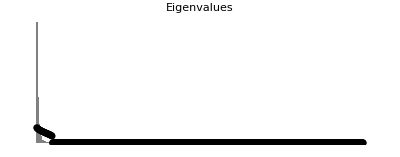
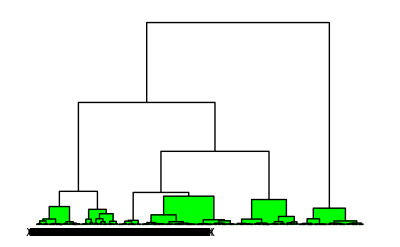
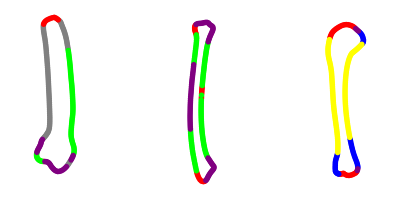
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 51.2255 |  | 
Relative Eigenvalue SD: 9.51234 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 6 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
FLMod=Modularity[FlightlessForeLimbProc,600,2,Labels,"RandomizationTest"];
ForeLimbFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
FLed=Prepend[Partition[Flatten[Table[StringSplit[mod[[X]],":"],{X,Length[mod]}]],2][[1;;,2]],"Flightless"];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

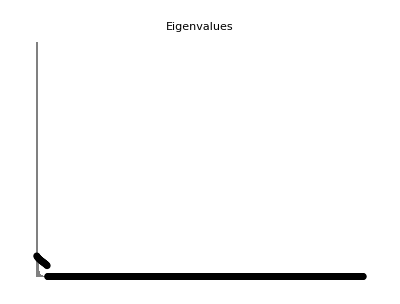
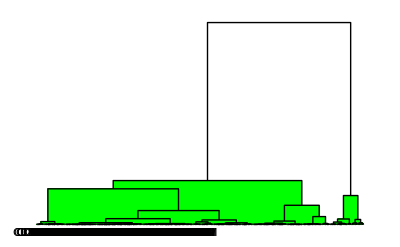
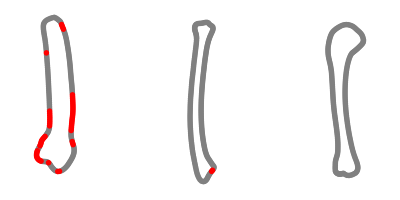
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 103.399 |  | 
Relative Eigenvalue SD: 23.1208 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.218218 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

Result

```mathematica
ForeLimbED=Partition[Join[getcolumnbTitles,Fed,FLed],5];
(*ForeLimbED//MatrixForm*)
```

```mathematica
FMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 51.2255 |  | 
Relative Eigenvalue SD: 9.51234 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 6 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 103.399 |  | 
Relative Eigenvalue SD: 23.1208 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.218218 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-